## Lab 7

For each function, plot the graph, and find the critical numbers and the local extrema if there is any.

f(x)=x^3-3x+3

```mathematica
f[x_]:=x^3-3x+3
cps=x/.NSolve[f'[x]==0,x,Reals]
```

{-1., 1.}

```mathematica
f[cps]
```

{5., 1.}

```mathematica
f''[cps]
```

{-6., 6.}

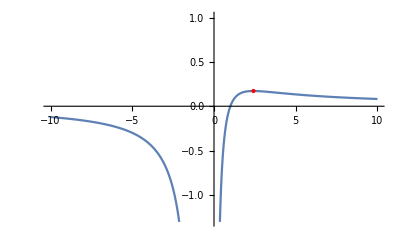

```mathematica
Show[{
Plot[f[x],{x,-10,10},PlotRange->Automatic],
Table[Graphics[{Red,PointSize[Medium],Point[{cps[[i]],f[cps[[i]]]}]}],{i,1,Length[cps]}]}]
```

f(x)=(x-1)/(x(x+1))

```mathematica
g[x_]:=(x-1)/(x*(x+1))
cps=x/.NSolve[g'[x]==0,x,Reals]
```

{-0.414214,2.41421}

```mathematica
g[cps]
```

{5.82843,0.171573}

```mathematica
g''[cps]
```

{48.0416,-0.0416306}

```mathematica
Show[{
Plot[g[x],{x,-10,10},PlotRange->Automatic],
Table[Graphics[{Red,PointSize[Medium],Point[{cps[[i]],g[cps[[i]]]}]}],{i,1,Length[cps]}]}]
```

-Graphics-

f(x)=(2x)/(x^2+1)

```mathematica
g[x_]:=(2x)/(x^2+1)
cps=x/.NSolve[g'[x]==0,x,Reals]
```

{-1.,1.}

```mathematica
g[cps]
```

{-1.,1.}

```mathematica
g''[cps]
```

{1.,-1.}

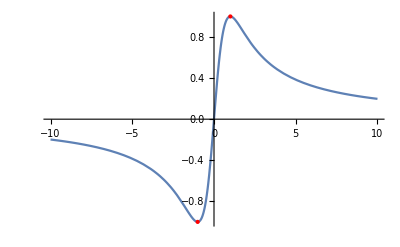

```mathematica
Show[{
Plot[g[x],{x,-10,10},PlotRange->Automatic],
Table[Graphics[{Red,PointSize[Medium],Point[{cps[[i]],g[cps[[i]]]}]}],{i,1,Length[cps]}]}]
```

For each function, plot the graph, and find the absolute extrema on the specified interval.

f(x)=(x+1)^2(x-2), [-2,2]

```mathematica
f[x_]:=(x+1)^2(x-2)
cps=x/.NSolve[f'[x]==0&&-2≤x≤2,x]
```

{-1.,1.}

```mathematica
xs=Sort[Flatten[{cps, -2,2}]]
```

{-2,-1.,1.,2}

```mathematica
fValues= f[xs]
```

{-4,0.,-4.,0}

```mathematica
Max[fValues]
```

0.

```mathematica
Min[fValues]
```

-4

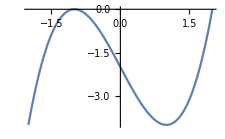

```mathematica
Show[{Plot[f[x],{x,-2,2},ImageSize->180],
Table[Graphics[{Red,PointSize[Medium],
Point[{xs[[iMaxs[[i]]]],fValues[[iMaxs[[i]]]]}]}],{i,1,Length[iMaxs]}],
Table[Graphics[{Blue,PointSize[Medium],
Point[{xs[[iMins[[i]]]],fValues[[iMins[[i]]]]}]}],{i,1,Length[iMins]}]}]
```

f(x)=sin x+2cos x, [-π,2π]

```mathematica
f[x_]:=Sin[x]+2Cos[x]
cps=x/.NSolve[f'[x]==0&&-Pi≤x≤2*Pi,x]
```

{-2.67795,0.463648,3.60524}

```mathematica
xs=Sort[Flatten[{cps,-Pi,2Pi}]]
```

{-2.67795,0.463648,3.60524,-π,2 π}

```mathematica
fValues= f[xs]
```

{-2.23607,2.23607,-2.23607,-2,2}

```mathematica
Max[fValues]
```

2.23607

```mathematica
Min[fValues]
```

-2.23607

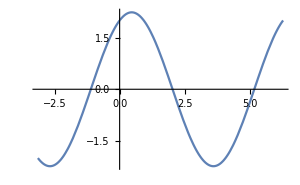

```mathematica
Show[{Plot[f[x],{x,-Pi,2Pi}],
Table[Graphics[{Red,PointSize[Medium],
Point[{xs[[iMaxs[[i]]]],fValues[[iMaxs[[i]]]]}]}],{i,1,Length[iMaxs]}],
Table[Graphics[{Blue,PointSize[Medium],
Point[{xs[[iMins[[i]]]],fValues[[iMins[[i]]]]}]}],{i,1,Length[iMins]}]}]
```

f(x)=x^2 sin 2x, [-π,π]

```mathematica
f[x_]:=x^2 Sin[2x]
cps=x/.NSolve[f'[x]==0&&-Pi≤x≤Pi,x]
```

{-2.54349,-1.14446,0.,1.14446,2.54349}

```mathematica
xs=Sort[Flatten[{cps,-Pi,2Pi}]]
```

{-2.54349,-1.14446,0.,1.14446,2.54349,-π,2 π}

```mathematica
fValues= f[xs]
```

{6.02074,-0.986325,0.,0.986325,-6.02074,0,0}

```mathematica
Max[fValues]
```

6.02074

```mathematica
Min[fValues]
```

-6.02074

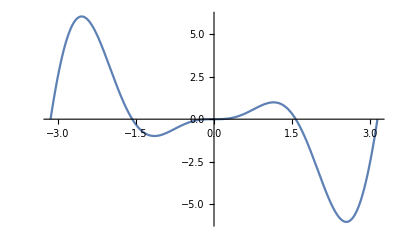

```mathematica
Show[{Plot[f[x],{x,-Pi,Pi}],
Table[Graphics[{Red,PointSize[Medium],
Point[{xs[[iMaxs[[i]]]],fValues[[iMaxs[[i]]]]}]}],{i,1,Length[iMaxs]}],
Table[Graphics[{Blue,PointSize[Medium],
Point[{xs[[iMins[[i]]]],fValues[[iMins[[i]]]]}]}],{i,1,Length[iMins]}]}]
```

Plot the graph of f(x)=ⅇ^-x cos 3x for -π≤x≤π. Then, use FindMaximum and FindMinimum to find all local extrema of the function on the interval. Note: You may have to use the option PlotRange to fine tune the graph.

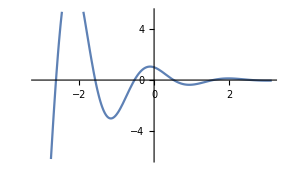

{0.130051,{x→1.98714}}

```mathematica
f[x_]:=ⅇ^-x Cos[3x];
Plot[f[x],{x,-π,π},PlotRange->Automatic]
FindMaximum[{f[x],-Pi≤ x≤ Pi},x]
FindMinimum[{f[x],-Pi≤ x≤ Pi},x]
```

```mathematica
{-0.370601,{x->0.93994}}
```

Refer to Example 6. Find the absolute extrema of f(x)=-ⅇ^((x-2)^2) on (0,∞).

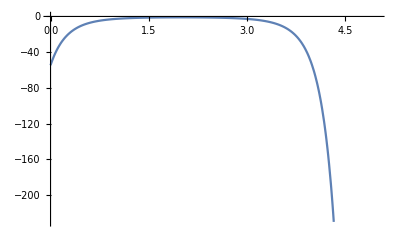

```mathematica
f[x_]:=-ⅇ^((x-2)^2)
Plot[f[x],{x,0,5},PlotRange->Automatic]
```

```mathematica
NSolve[f'[x]==0&&x>0,x]
```

{{x→2.}}

```mathematica
f''[2]
```

-2

is negative, so f(x) is concave downward on (0,∞).

```mathematica
f[2]
```

-1

is the absolute maximum value over (0,∞).There is no absolute minimum value which can be confirmed when taking the limit.

Refer to Example 6. Find the point(s) on the curve of y=1/x which has the shortest distance to the origin.

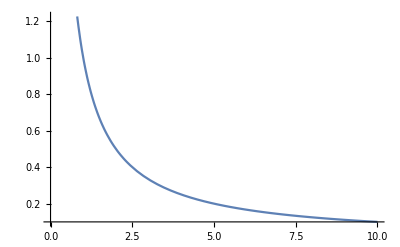

```mathematica
f[x_]:=1/x
Plot[f[x],{x,0,10},PlotRange->Automatic]
```

```mathematica
f[x_]:=√(x^2+1/x^2)
NSolve[f'[x]==0&&x>0,x]
```

{{x→1.}}

```mathematica
f''[1]
```

2 √2

```mathematica
f[1]
```

√2

The shortest distance on the curve to the origin is when f[1]=√2.

Find the dimensions of the largest and closed rectangular box with a surface area of 100 cm^2, given that one dimension is twice as large as another dimension.

```mathematica
A[w_]=w*2w*((50-2 w^2)/(3w))
```

```mathematica
w/. NSolve[A'[w]==0,w]
```

{-2.88675,2.88675}

```mathematica
Max[{-2.8867513459481287,2.886751345948129}]
```

2.88675

The max value of the width is 2.88675cm . Plugging this number back into the original values, we get length=5.7735cm and height = 3.849 cm .

Find the dimensions of the largest and closed circular cylinder with a surface area of 100 cm^2.

```mathematica
V[r_]=50*r-(Pi*r^3)
```

50 r-π r^3

```mathematica
r/.NSolve[V'[r]==0,r]
```

{-2.30329,2.30329}

```mathematica
Max[{-2.3032943298089035,2.303294329808903}]
```

2.30329

```mathematica
V[2.303294329808903]
```

76.7765

Here we see that the max volume is 76.7765 cm^3. We know that h=V/πr^2 so plugging the volume into this equation we get h=4.6066 cm and r=2.30329cm.

Find the dimensions of the largest rectangle that is bounded by x=0, x=2, y=1, and y=ⅇ^(x/2).

```mathematica
f[x_]:=ⅇ^(x/2)
A[x_]=x*(ⅇ^(x/2)-1)//Simplify
```

(-1+ⅇ^(x/2)) x

```mathematica
APrime[x_]=A'[x]
```

-1+ⅇ^(x/2)+1/2 ⅇ^(x/2) x

```mathematica
cps=x/.NSolve[APrime[x]==0&&0≤x≤2,x]
```

{0.}

```mathematica
A[{0,cps,2}]
```

{0,{0.},2 (-1+ⅇ)}

The largest rectangle has a width of 2(-1+e) or 3.4366 units and plugging that into f(x) the length would be 5.575 units

(Optional) Write code to generate and print random integer numbers in the range from 1 to 10 until the number 5 is generated. Do not print 5.

```mathematica
Do[Print[RandomInteger[10]],5]
```

0

4

2

5

0

(Optional) Write code to print the following 9 x 9 multiplication table.

```mathematica
Do[
Apply[Print,
Table[
StringJoin[ToString[i],"×",ToString[j],"=",
If[i*j<10,StringJoin[ToString[i*j]," "],ToString[i*j]]," "],
{j,9}]],
{i,9}]
```

1×1=1  1×2=2  1×3=3  1×4=4  1×5=5  1×6=6  1×7=7  1×8=8  1×9=9

2×1=2  2×2=4  2×3=6  2×4=8  2×5=10 2×6=12 2×7=14 2×8=16 2×9=18

3×1=3  3×2=6  3×3=9  3×4=12 3×5=15 3×6=18 3×7=21 3×8=24 3×9=27

4×1=4  4×2=8  4×3=12 4×4=16 4×5=20 4×6=24 4×7=28 4×8=32 4×9=36

5×1=5  5×2=10 5×3=15 5×4=20 5×5=25 5×6=30 5×7=35 5×8=40 5×9=45

6×1=6  6×2=12 6×3=18 6×4=24 6×5=30 6×6=36 6×7=42 6×8=48 6×9=54

7×1=7  7×2=14 7×3=21 7×4=28 7×5=35 7×6=42 7×7=49 7×8=56 7×9=63

8×1=8  8×2=16 8×3=24 8×4=32 8×5=40 8×6=48 8×7=56 8×8=64 8×9=72

9×1=9  9×2=18 9×3=27 9×4=36 9×5=45 9×6=54 9×7=63 9×8=72 9×9=81

(Optional) Write code to print the following 9 x 9 multiplication table.

```mathematica
Do[
Apply[Print,
Table[
StringJoin[ToString[i],"×",ToString[j],"=",
If[i*j<10,StringJoin[ToString[i*j]," "],ToString[i*j]]," "],
{j,9}]],
{i,9}]
```

1×1=1  1×2=2  1×3=3  1×4=4  1×5=5  1×6=6  1×7=7  1×8=8  1×9=9

2×1=2  2×2=4  2×3=6  2×4=8  2×5=10 2×6=12 2×7=14 2×8=16 2×9=18

3×1=3  3×2=6  3×3=9  3×4=12 3×5=15 3×6=18 3×7=21 3×8=24 3×9=27

4×1=4  4×2=8  4×3=12 4×4=16 4×5=20 4×6=24 4×7=28 4×8=32 4×9=36

5×1=5  5×2=10 5×3=15 5×4=20 5×5=25 5×6=30 5×7=35 5×8=40 5×9=45

6×1=6  6×2=12 6×3=18 6×4=24 6×5=30 6×6=36 6×7=42 6×8=48 6×9=54

7×1=7  7×2=14 7×3=21 7×4=28 7×5=35 7×6=42 7×7=49 7×8=56 7×9=63

8×1=8  8×2=16 8×3=24 8×4=32 8×5=40 8×6=48 8×7=56 8×8=64 8×9=72

9×1=9  9×2=18 9×3=27 9×4=36 9×5=45 9×6=54 9×7=63 9×8=72 9×9=81